# Test Problems for the GEP Algorithm

## 2D with pics

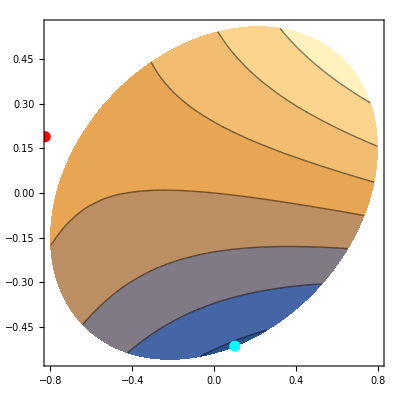

```mathematica
m=2;
A=RandomReal[{-1,1},{m,m}];A=A+Aᵀ;
B=RandomReal[{-1,1},{m,m}];B=B.Bᵀ;
g=RandomReal[{-1,1},m];
Δ=0.7;
Ω=ImplicitRegion[{x,y}.B.{x,y}≤Δ^2,{x,y}];
{pStarBI}=NArgMin[{0.5*p.A.p+g.p,p.B.p≤Δ^2},p];
pCP=LinearSolve[A,-g];
M0=ArrayFlatten[({{{{Δ^2}}, 0, {g}}, {0, -B, A}, {{g}ᵀ, A, 0}})];
M1=ArrayFlatten[({{{{0}}, 0, 0}, {0, 0, B}, {0, B, 0}})];
M0Twiddle=ArrayFlatten[({{-B, A}, {A, -KroneckerProduct[g,g]/Δ^2}})];
M1Twiddle=ArrayFlatten[({{0, B}, {B, 0}})];
λs=Eigenvalues[{M0Twiddle,-M1Twiddle}];
λ=Re[Sort[λs,Re[#1]<Re[#2]&]⟦-1⟧];
pEdge=LinearSolve[A+λ B, -g];
ContourPlot[0.5*{x,y}.A.{x,y}+g.{x,y},{x,y}∈Ω,
Epilog->{
{Red,PointSize[0.02],Point[pCP]},
{Cyan, PointSize[0.02],Point[pEdge]}
}]
```

Making three 2D test problems

```mathematica
SetDirectory["C:\\Users\\struther\\Desktop\\2022-23-Classes\\MA5630"]
```

C:\Users\struther\Documents\TRSGEPTestProblemA

```mathematica
SetDirectory["C:\\Users\\struther\\Desktop\\2022-23-Classes\\MA5630"]
Tag="C";
DirName=StringJoin["TRSGEPTestProblem",Tag];
CreateDirectory[DirName];
SetDirectory[DirName];
Directory[]
ResetDirectory[]
Directory[]
```

C:\Users\struther\Desktop\2022-23-Classes\MA5630

C:\Users\struther\Desktop\2022-23-Classes\MA5630\TRSGEPTestProblemC

C:\Users\struther\Desktop\2022-23-Classes\MA5630

C:\Users\struther\Desktop\2022-23-Classes\MA5630

```mathematica
Directory[]
```

C:\Users\struther\Desktop\2022-23-Classes\MA5630\TRSGEPTestProblemA

```mathematica
Clear[A,B,g,Δ,pStarBI,pCP,pEdge]
m=2;
A=RandomReal[{-1,1},{m,m}];A=A+Aᵀ;
B=RandomReal[{-1,1},{m,m}];B=B.Bᵀ;
g=RandomReal[{-1,1},m];
Δ=0.7;
AbsoluteTiming[{val,sub}=FindMinimum[{0.5*p.A.p+g.p,p.B.p≤Δ^2},p];];
pStarBI=p/.sub;
pCP=LinearSolve[A,-g];
M0Twiddle=ArrayFlatten[({{-B, A}, {A, -KroneckerProduct[g,g]/Δ^2}})];
M1Twiddle=ArrayFlatten[({{0, B}, {B, 0}})];
λs=Eigenvalues[{M0Twiddle,-M1Twiddle}];
λ=Re[Sort[λs,Re[#1]<Re[#2]&]⟦-1⟧];
pEdge=LinearSolve[A+λ B, -g];
TableForm[{
Map[FullForm[0.5 #.A.# + g.# ]&,{pCP,pEdge,pStarBI}],
Map[#.B.# -Δ^2 &,{pCP,pEdge,pStarBI}]
},TableHeadings->{{"f","cons"},{"pCP","pEdge","pStarBI"}}]
```

| pCP | pEdge | pStarBI
f | -0.00453451 | -27.2508 | -26.7189
cons | -0.487976 | 2.76446×10^-13 | 8.34105×10^-9

## 3D with pics

```mathematica
m=3;
A=RandomReal[{-1,1},{m,m}];A=A+Aᵀ;
B=RandomReal[{-1,1},{m,m}];B=B.Bᵀ;
g=RandomReal[{-1,1},m];
f[p_]:=0.5p.A.p+g.p
Δ=0.7;
Ω=ImplicitRegion[{x,y,z}.B.{x,y,z}≤Δ^2,{x,y,z}];
{pStarBI}=NArgMin[{0.5*p.A.p+g.p,p.B.p≤Δ^2},p];
pCP=LinearSolve[A,-g];
M0=ArrayFlatten[({{{{Δ^2}}, 0, {g}}, {0, -B, A}, {{g}ᵀ, A, 0}})];
M1=ArrayFlatten[({{{{0}}, 0, 0}, {0, 0, B}, {0, B, 0}})];
M0Twiddle=ArrayFlatten[({{-B, A}, {A, -KroneckerProduct[g,g]/Δ^2}})];
M1Twiddle=ArrayFlatten[({{0, B}, {B, 0}})];
λs=Eigenvalues[{M0Twiddle,-M1Twiddle}];
λ=Re[Sort[λs,Re[#1]<Re[#2]&]⟦-1⟧];
pEdge=LinearSolve[A+λ B, -g];
Show[
ContourPlot3D[0.5*{x,y,z}.A.{x,y,z}+g.{x,y,z},{x,y,z}∈Ω,
Contours->7,PlotPoints->50,
PlotLegends->Automatic],
Graphics3D[{
{Red,PointSize[0.02],Point[pCP]},
{Cyan, PointSize[0.02],Point[pEdge]}
}]
]
TableForm[{
Map[FullForm[0.5 #.A.# + g.# ]&,{pCP,pEdge,pStarBI}],
Map[#.B.# -Δ^2 &,{pCP,pEdge,pStarBI}]
},TableHeadings->{{"f","cons"},{"pCP","pEdge","pStarBI"}}]
```

-Graphics3D-

| pCP | pEdge | pStarBI
f | -0.313753 | -4.95602 | -4.95602
cons | -0.365176 | 3.48055×10^-14 | 0.

## Dimension m no pics

```mathematica
m=100;
A=RandomReal[{-1,1},{m,m}];A=A+Aᵀ;
B=RandomReal[{-1,1},{m,m}];B=B.Bᵀ;
g=RandomReal[{-1,1},m];
f[p_]:=0.5p.A.p+g.p
AbsoluteTiming[{val,sub}=FindMinimum[{0.5*p.A.p+g.p,p.B.p≤Δ^2},p];]
pStarBI=p/.sub;
AbsoluteTiming[
pCP=LinearSolve[A,-g];
M0Twiddle=ArrayFlatten[({{-B, A}, {A, -KroneckerProduct[g,g]/Δ^2}})];
M1Twiddle=ArrayFlatten[({{0, B}, {B, 0}})];
{λs,Vs}=Eigensystem[{M0Twiddle,-M1Twiddle}];
λVs={λs,Vs}ᵀ;
{λMax,vMax}=Chop[Sort[λVs,Re[#1⟦1⟧]<Re[#2⟦1⟧]&]⟦-1⟧];
{y1,y2}=Partition[vMax,m];
p1=-Sign[g.y2]*Δ*y1/√(y1.B.y1);
(*p1=LinearSolve[A+λMax B, -g];*)
]
TableForm[{
Map[FullForm[0.5 #.A.# + g.# ]&,{pCP,p1,pStarBI}],
Map[#.B.# -Δ^2 &,{pCP,p1,pStarBI}]
},TableHeadings->{{"f","cons"},{"pCP","p1","pStarBI"}}]
```

{3.70023,Null}

{0.0592616,Null}

| pCP | p1 | pStarBI
f | 2.96215 | -386.478 | -386.478
cons | 926.232 | -2.67219×10^-11 | 1.19459×10^-8